# THE SC construction for the unit triangle 0, 1, ⅈ from the pre-vertices 0, 1, and -1

I need to find an f that matches. 
	f'(z)=C (z+1)^(-1/2)(z^(-3/4)(z-1))^(-3/4).
We need f to be analytic in the upper half plane.  A symbolic integration does not necessarily respect these branch cuts.  It is also #$#@ slow.

```mathematica
fPrime[0.0]=0.0;
fPrime[z_]:=(z+1)^(-1/2)(z^(-3/4)(z-1))^(-3/4)
Integrate[fPrime[z],z]
f1[z_]:=(16 (1-z)^(3/4) z AppellF1[25/16,3/4,1/2,41/16,z,-z])/(25 ((-1+z)/z^(3/4))^(3/4))
```

(16 (1-z)^(3/4) z AppellF1[25/16,3/4,1/2,41/16,z,-z])/(25 ((-1+z)/z^(3/4))^(3/4))

Note (as shown below) the “very-special” function AppellF1
	https://en.wikipedia.org/wiki/Appell_series
is a thousand times slower than the functions you are used to.  There may (or may not) be a good reason for this! See the discussions concerning Python at https://github.com/mpmath/mpmath/issues/633 and Mathematica at https://mathematica.stackexchange.com/questions/298554/abnormally-long-computation-time-using-appellf1-function.

```mathematica
z0=RandomComplex[{-1-I,1+I}];
AbsoluteTiming[f1[z0]]
10^3*{AbsoluteTiming[fPrime[z0];],AbsoluteTiming[Cos[z0];],AbsoluteTiming[Cos[Log[Sin[z0]]];]}
```

{0.0280886,0.594441+0.397247 ⅈ}

{{0.0124,1000 Null},{0.0127,1000 Null},{0.0041,1000 Null}}

Do not attempt to plot  AppellF1 unless you have a several spare minutes! Search “Why is AppellF1 slow?” in Google for an explanation.  The plot below shows the derivative function is automatically nice in the upper half plane and has lim_(z->0) f(z)=0.

```mathematica
TabView[{
"Close-Up Origin"->ComplexPlot3D[fPrime[z],{z,2}],
"Upper-Half Plane"->ComplexPlot3D[fPrime[z],{z, -5+0.2 I ,5+3 I},PlotRange->{0,1.5},MaxRecursion->8]
}]
```

```mathematica
12
```

We can avoid the @#@# function by just integrating the derivative f' directly.  Since F(z)=∫_0^z f'(ζ)dζ is independent of path in the upper half plane if we have a regularly spaced grid of value of the derivative f' then we can use horizontal aka real trapezoid steps
	f(x+Δx + ⅈ y)≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ Δx + ⅈ y))/2 Δx
and vertical aka imaginary trapezoid steps
	f(x + ⅈ (y+Δy))≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ ⅈ (y+Δy)))/2 ⅈ Δy
to step to any grid point starting from f(0)=0.  The branch cuts along the real axis suggest we first step up vertically from the origin to build a table of values along the positive imaginary axis. We can then step of the imaginary axis (in the positive and negative directions) to fill in the values of f on horizontal lines.   For the numerically inclined it is indeed true that it would be better to think about this in the centered form 
	f(x+Δx/2 + ⅈ y)≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ Δx + ⅈ y))/2 Δx
	f(x + ⅈ (y+Δy/2))≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ ⅈ (y+Δy)))/2 ⅈ Δy.

I want this to look good at the end!  In this context this means that:

I need lots of values near the real axis y = 0 which is the boundary of the triangle!

I need lots of values near the singularities aka pre-vertices x=-1,0,1 which are the corners of the triangle.

I need to get well out the real axis to fill in the last edge of the triangle.

I need to get well out the positive imaginary axis to fill in the middle of the triangle.

To do this with a reasonable number of points we need a grid with different sized gaps.

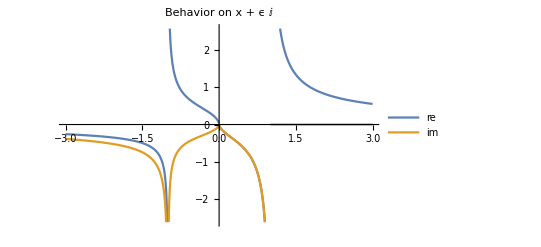

```mathematica
ϵ=10^-12;
Plot[{Re[fPrime[x + ϵ ⅈ]],Im[fPrime[x]]},{x,-3,3},
PlotLegends->{"re","im"},
PlotLabel->"Behavior on x + ϵ ⅈ"]
```